```mathematica
α[i_]:=BesselJZero[1, i]
α[0]:=0
```

```mathematica
β[i_]:=BesselJZero[0,i]
```

```mathematica
mat[Nmax_,S_]:=Table[2/S BesselJ[0,1/S α[i]α[j]]/(Abs[BesselJ[0,α[i]]]Abs[BesselJ[0,α[j]]]),{i,0,Nmax},{j,0,Nmax}]
```

```mathematica
matDirichlet[Nmax_,S_]:=Table[2/S BesselJ[0,1/S β[i]β[j]]/Abs[BesselJ[1,β[i]]BesselJ[1,β[j]]],{i,1,Nmax+1},{j,1,Nmax+1}]
```

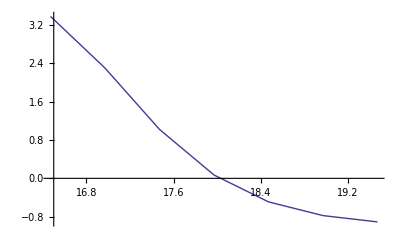

```mathematica
ListLinePlot[Table[{S,Abs[Det[mat[5,S].mat[5,S]]]-1},{S,17.9,18.1,0.5}]]
```

```mathematica
Abs[Det[mat[5,S].mat[5,S]]]-1/.S->18
```

0.02699618730800097100158382

```mathematica
FindRoot[Abs[Det[mat[5,S].mat[5,S]]]-1,{S,18}]
```

{S→18.019}

```mathematica
Abs[Det[mat[5,S]]]-1/.Out[9]
```

2.22045×10^-15

```mathematica
Max[Abs[mat[5,S].mat[5,S]-IdentityMatrix[6]]]/.Out[9]
```

1.00051

```mathematica
mat[5,S].mat[5,S]-IdentityMatrix[6]/.Out[9]//MatrixForm
```

$Aborted

```mathematica
Max[Abs[(mat[5,S].mat[5,S]/.Out[9])-IdentityMatrix[6]]]
```

0.00060191

```mathematica
mat[5,S
```

```mathematica
z=(mat[5,S].mat[5,S]/.Out[9])-IdentityMatrix[6]
```

{{0.000178313,-0.000162692,0.000121704,-0.0000433947,-0.0000978165,0.000355579},{-0.000162692,0.000147215,-0.000106524,0.0000284879,0.000113151,-0.000374494},{0.000121704,-0.000106524,0.0000664657,0.0000109654,-0.000153481,0.000422757},{-0.0000433947,0.0000284879,0.0000109654,-0.0000877498,0.000230936,-0.000507207},{-0.0000978165,0.000113151,-0.000153481,0.000230936,-0.000370576,0.00060191},{0.000355579,-0.000374494,0.000422757,-0.000507207,0.00060191,0.0000676561}}

```mathematica
√Total[z^2,∞]
```

0.0016269

```mathematica
Frobenius[Nmax_,S_]:=With[{z = mat[Nmax,S]},With[{Z=z.z - IdentityMatrix[Nmax+1]},√Total[Z^2,∞]]]
```

```mathematica
Clear[FrobeniusDirichlet]
```

```mathematica
FrobeniusDirichlet[Nmax_,S_]:=With[{z = matDirichlet[Nmax,S]},With[{Z=z.z-IdentityMatrix[Nmax+1]},√Total[Z^2,∞]]]
```

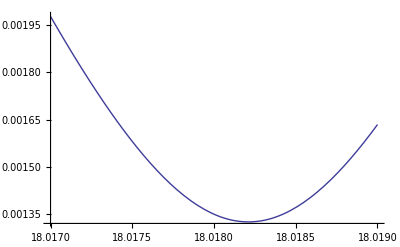

```mathematica
Plot[Frobenius[5,S],{S,18.017,18.019}]
```

```mathematica
Eigenvalues[mat[5,S]/.Out[9]]
```

{1.00053,-1.00009,1.,-1.,1.,-0.999386}

```mathematica
N[{β[6],β[7],β[8]}]
```

{18.0711,21.2116,24.3525}

```mathematica
Plot[FrobeniusDirichlet[5,S],{S,21.21165,21.21168}]
```

$Aborted

```mathematica
FindMinimum[FrobeniusDirichlet[5,S],{S,21.21163662987926},WorkingPrecision->60]
```

{2.2319317785450758031992841223401541559221797241102831351963×10^-7,{S→21.2116317173116196401477859288666104611744026736436818153817}}

```mathematica
FindMinValue[FrobeniusDirichlet[5,S],{S,21.21163662987926},WorkingPrecision->30]
```

2.23193177854507580319956087467×10^-7

```mathematica
FindMinValue[Frobenius[5,S],{S,18},WorkingPrecision->60]
```

0.0013248697275753121905214326934861311611500216254792116598834

```mathematica
MinValueNeumann[Nmax_]:=FindMinValue[Frobenius[Nmax,S],{S,1/2(α[Nmax]+α[Nmax+1])},WorkingPrecision->30]
```

```mathematica
MinValueDirichlet[Nmax_]:=FindMinValue[FrobeniusDirichlet[Nmax,S],{S,β[Nmax+2]},WorkingPrecision->30]
```

```mathematica
MinValueDirichlet2[Nmax_]:=FindMinValue[FrobeniusDirichlet[Nmax,S],{S,1/2(β[Nmax+1]+β[Nmax+2])},WorkingPrecision->30]
```

```mathematica
MinValueNeumann[6]
```

0.00118992210152733591497170028049

```mathematica
MinValueDirichlet[6]
```

1.86199516976746925617906449947×10^-7

```mathematica
is=Table[2^i,{i,2,7}]
```

{4,8,16,32,64,128}

```mathematica
neumannData=Table[{Log[Nmax+1],Log[MinValueNeumann[Nmax]]},{Nmax,is}];
```

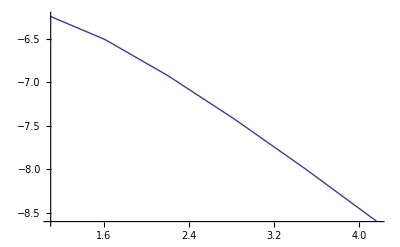

```mathematica
ListLinePlot[neumannData]
```

```mathematica
Normal[LinearModelFit[neumannData,x,x]]
```

-5.28674743110437172376951760984-0.776956179338809608698838131573 x

```mathematica
DirichletData=Table[{Log[Nmax+1],Log[MinValueDirichlet[Nmax]]},{Nmax,is}];
```

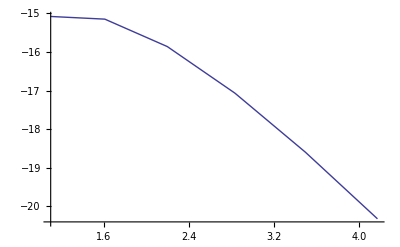

```mathematica
ListLinePlot[DirichletData]
```

```mathematica
Normal[LinearModelFit[DirichletData,x,x]]
```

-12.4913541922450900300514715446-1.76060511724168161098953814573 x

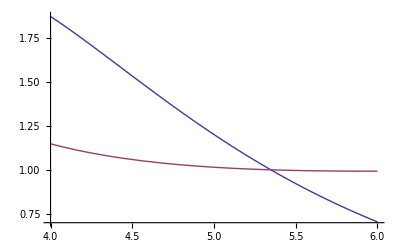

```mathematica
Plot[Evaluate[Abs[Eigenvalues[mat[1,S]]]],{S,4,6}]
```

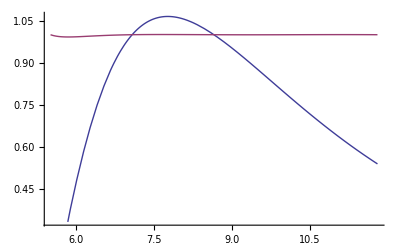

```mathematica
Plot[Evaluate[Abs[Eigenvalues[matDirichlet[1,S]]]],{S,β[2],β[4]}]
```

```mathematica
FullSimplify@Eigenvalues[mat[1,S]]
```

{1/S+(S BesselJ[0,BesselJZero[1,1]^2/S]-√(S^2 (BesselJ[0,BesselJZero[1,1]]^4+BesselJ[0,BesselJZero[1,1]]^2 (4-2 BesselJ[0,BesselJZero[1,1]^2/S])+BesselJ[0,BesselJZero[1,1]^2/S]^2)))/(S^2 BesselJ[0,BesselJZero[1,1]]^2),(S (BesselJ[0,BesselJZero[1,1]]^2+BesselJ[0,BesselJZero[1,1]^2/S])+√(S^2 (BesselJ[0,BesselJZero[1,1]]^4+BesselJ[0,BesselJZero[1,1]]^2 (4-2 BesselJ[0,BesselJZero[1,1]^2/S])+BesselJ[0,BesselJZero[1,1]^2/S]^2)))/(S^2 BesselJ[0,BesselJZero[1,1]]^2)}

```mathematica
N[1/2(α[1]+α[2])]
```

5.42365

```mathematica
N[{β[2],β[3],β[4]}]
```

{5.52008,8.65373,11.7915}

```mathematica
N[{1/2(β[2]+β[3])}]
```

{7.0869}